# Amplitude Pulse-Shaping Last Updated: 5/24/2021

```mathematica
Quit[]
```

```mathematica
Remove["Global`*"];ClearInOut[];
```

## 0 Prep

## 0.0 Setup

### 0.0.1 User Config

```mathematica
(*user input*)
	(*enter chain configuration*)
(*mArr={mMol,mMol};*)
```

```mathematica
mArr={mMol,mMol,mMol,mMol,mAtom};
```

### 0.0.2 Config - RDX

```mathematica
(*qubits*)
numIons=Length[mArr];
```

```mathematica
(*ion positions*)
indMol:=Position[mArr,mMol]//Flatten;
indAtom:=Position[mArr,mAtom]//Flatten;
```

### 0.0.3 Useful Functions

```mathematica
Off[General::munfl];
```

```mathematica
(*play sound when finished*)
Done[type_:"none",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}],message="Calc Done"},
Switch[type,
"text",SendMessage["SMS",message],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->"Calc Done: "<>ToString[msg],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Password"->"I2Ic1zIS2R"|>],
"none",EmitSound[soundDJ]];];
```

## 0.1 Values

### 0.1.1 Constants

```mathematica
(*fundamental*)
ℏ=1.0545718*^-34;me=9.10938356*^-31;qe=1.60217662*^-19;c=2.99792458*^8;kb=1.38064852*^-23;
```

```mathematica
(*derived*)
ke2=2.30707751*^-28;a0=ℏ^2/me/ke2;
```

```mathematica
(*defined*)
amu=1.66053904*^-27;wghz=2π 1.*^9;wmhz=2π 1.*^6;wkhz=2π 1.*^3;debye=1.*^-21/c;μs=1.*^-6;mm=1.*^-3;nm=1.*^-9;
```

### 0.1.2 Variables

```mathematica
(*mMol=38*amu;mAtom=40*amu;*)
```

```mathematica
mMol=171*amu;mAtom=138*amu;
Δk=N[2*^9*2π/(mArr/.{mMol->355,mAtom->532})];
```

### 0.1.3 Quick Eigen

#### 0.2.3.1 in terms of ω_(sec-Mol), fixed ω_sec

```mathematica
wsecMol={3.06,0.16}*wmhz;
wsecAtom:={Sqrt[((wsecMol[[1]])^2+0.5*(#)^2)*(mMol/mAtom)^2-0.5*(#)^2*mMol/mAtom],#*Sqrt[mMol/mAtom]}&[wsecMol[[2]]];
(*wsecMol={3.06,1.23}*wmhz;*)
(*wsecMol={Sqrt[3.06^2+(0.16^2-#^2)/2],#}*wmhz&[1.117];
wsecMol/wmhz*)
```

```mathematica
(*ωRF=40*wmhz;
qMol=2/ωRF √(2*wsecMol[[1]]^2+wsecMol[[2]]^2);qAtom=2/ωRF √(2*wsecAtom[[1]]^2+wsecAtom[[1]]^2);
qMol*)
```

#### 0.2.3.2 in terms of trap parameters

```mathematica
(*VRF=342.8;ωRF=28.25*wmhz;κr=1;r0=0.41278*mm;
z0=0.2*mm;κz=1;U=0.1433;
qMol:=(2*qe*(VRF*κr))/(mMol*ωRF^2*r0^2);qAtom:=(2*qe*(VRF*κr))/(mAtom*ωRF^2*r0^2);
wsecMol:=ωRF/2*Sqrt[{qMol^2/2-#,2.*#}]&[(4*qe*U*κz)/(z0^2*mMol*ωRF^2)];wsecAtom:=ωRF/2*Sqrt[{qAtom^2/2-#,2.*#}]&[(4*qe*U*κz)/(z0^2*mAtom*ωRF^2)];
wsecMol/wmhz*)
```

#### 0.2.3.3 Find Eigen

```mathematica
(*get individual secular frequencies*)
wsecvalsMAT=Transpose[mArr/.{mMol->wsecMol}/.{mAtom->wsecAtom}];
```

```mathematica
(*Calculate equilibrium positions (axial crystal)*)
z0eqArr = Array[z0eq,numIons];l0:=(ke2/(mMol*wsecMol[[2]]^2))^(1/3);
L0EQlist=z0eqArr[[#]]==(Sum[(z0eqArr[[#]] - z0eqArr[[k]])^(-2),{k,1,#-1}] - Sum[(z0eqArr[[#]] - z0eqArr[[k]])^(-2),{k, #+1,numIons}])&/@Range[numIons];
guessz0eq=Range[-#,#,2*#/(numIons-1)]&[numIons^(1/3)]//N;guessz0eq=Transpose[Join[{z0eqArr},{guessz0eq}]];
z0eqArr=z0eqArr/.Chop[FindRoot[L0EQlist,guessz0eq]];
L0Mn=Abs[Table[If[i==j,0,(z0eqArr[[i]]-z0eqArr[[j]])^(-3)],{i,numIons},{j,numIons}]];
```

```mathematica
(*Create matrices*)
VMatZ=Table[Sqrt[mArr[[i]]/mArr[[j]]]*wsecvalsMAT[[2,i]]^2*If[i==j,1+2*Sum[L0Mn[[i,id]],{id,numIons}],-2*L0Mn[[i,j]]],{i,numIons},{j,numIons}];
VMatX=Table[Sqrt[mArr[[i]]/mArr[[j]]]*wsecvalsMAT[[2,i]]^2*If[i==j,(wsecvalsMAT[[1,i]]/wsecvalsMAT[[2,i]])^2-Sum[L0Mn[[i,id]],{id,numIons}],L0Mn[[i,j]]],{i,numIons},{j,numIons}];
(*get eigen*)
eigenholder={Eigensystem[VMatX],Eigensystem[VMatZ]};
wmvals=Sqrt[eigenholder[[;;,1]]];vmvals:=eigenholder[[;;,2]];
{vmvals[[#1]]//MatrixForm,wmvals[[#1]]/wmhz//MatrixForm}&[1]
```

{(0.000139932 | 0.00035352 | 0.00113059 | 0.00723175 | 0.999973
-0.631341 | -0.547561 | -0.450906 | -0.313465 | 0.00305869
0.679189 | -0.0741916 | -0.475781 | -0.553904 | 0.00447492
-0.35765 | 0.6745 | 0.122543 | -0.634115 | 0.00425892
0.110439 | -0.489615 | 0.745183 | -0.439063 | 0.0024904),(3.78578
3.05884
3.05216
3.04352
3.03399)}

```mathematica
(*wmvals={{3.403,3.062,3.056,3.048,3.039},{0.57,0.48,0.387,0.279,0.158}}*wmhz;*)
```

#### 0.2.3.4 Lamb-Dicke

```mathematica
η=√(ℏ/2.)Table[Δk[[i]]/(√(mArr[[i]]*wmvals[[d,q]]))*vmvals[[d,q,i]],{d,2},{i,numIons},{q,numIons}];
```

## 1 AM Pulse-Shaping

## 1.1 Setup

### 1.1.1 Pulse Shape

```mathematica
numPulses=5;pulseTime=200*μs;
```

```mathematica
pulseVec=Array[Ω,numPulses];
tArr=Range[0,pulseTime,pulseTime/numPulses];
```

### 1.1.2 Spin-Motion Conditions

```mathematica
Aim[u_Real,ion_Integer,mode_Integer,dir_Integer]:=With[{w=wmvals[[dir,mode]]},
(η[[dir,ion,mode]]/(u^2-w^2))*((#1[[2;;]]-#1[[;;-2]])&[Exp[ⅈ*w*tArr]*(u*Cos[u*tArr]-ⅈ*w*Sin[u*tArr])])]
```

```mathematica
Bkl[u_,temp_,ions_,dir_]:=With[{AimMat={{Aim[u,ions[[1]],#,dir]},{Aim[u,ions[[2]],#,dir]}}&/@Range[numIons]},
(*1/4**)(βk[temp,dir,wmvals[[dir]]]).Apply[Plus,Map[ConjugateTranspose[#].#&,AimMat,{2}],1]]
```

### 1.1.3 Entanglement Conditions

```mathematica
XklInd[u_,mode_,dir_]:=Module[{w=wmvals⟦dir,mode⟧,up=u+wmvals⟦dir,mode⟧,um=u-wmvals⟦dir,mode⟧,upper1,upper2,diag1,upperMat,diagMat},
upper1=((up*Sin[um*#1]-um*Sin[up*#1])/(2 (up*um))&)/@tArr;upper2=-((up Cos[um #1]+um Cos[up #1])/(2 (up*um))&)/@tArr;diag1=1/(4 (up*um))((2 w u #1+u Sin[2 w #1]-w Sin[2 u #1])/u-(um^2 Sin[2 up #1]+up^2 Sin[2 um #1])/(2 (up*um)))&/@tArr;upperMat=(LowerTriangularize[Transpose[#1]-#1]&)[KroneckerProduct[upper1⟦2;;All⟧-upper1⟦1;;-2⟧,upper2⟦2;;All⟧-upper2⟦1;;-2⟧]];diagMat=(DiagonalMatrix[(#1⟦2;;All⟧+#1⟦1;;-2⟧) (#2⟦2;;All⟧-#2⟦1;;-2⟧)-(#3⟦2;;All⟧-#3⟦1;;-2⟧)]&)[upper1,upper2,diag1]; 
2(upperMat+diagMat(*+Transpose[upperMat]*))]
```

```mathematica
Xkl[u_,ions_List,dir_Integer]:=Times@@η⟦dir,ions,Range[numIons]⟧.(XklInd[u,#1,dir]&)/@Range[numIons]
```

### 1.1.4 Fidelity

```mathematica
(*phonon number*)
βk=Compile[{{temp,_Real},{dir,_Integer},{w,_Real,1}},
Coth[3.81911755498*^-12*w/temp],CompilationTarget->"C"];
```

```mathematica
(*for fidelity*)
Gi[u_,temp_,vec_,ion_,dir_]:=Exp[((-βk[temp,dir,wmvals[[dir]]])/2).Abs[((Aim[u,ion,#,dir]&/@Range[numIons]).vec)]^2]
Gp[u_,temp_,vec_,ions_,dir_]:=Exp[((-βk[temp,dir,wmvals[[dir]]])/2).Abs[(((Aim[u,ions[[1]],#,dir]+Aim[u,ions[[2]],#,dir])&/@Range[numIons]).vec)]^2]
Gm[u_,temp_,vec_,ions_,dir_]:=Exp[((-βk[temp,dir,wmvals[[dir]]])/2).Abs[(((Aim[u,ions[[1]],#,dir]-Aim[u,ions[[2]],#,dir])&/@Range[numIons]).vec)]^2]
```

```mathematica
(*actual fidelity*)
Fid[u_,temp_,vec_,ions_,dir_]:=1/8*(2+2*(Gi[u,temp,vec,ions[[1]],dir]+Gi[u,temp,vec,ions[[2]],dir])+(Gp[u,temp,vec,ions,dir]+Gm[u,temp,vec,ions,dir]));
```

## 1.2 Generalized Eigenvalue Problem

```mathematica
(*set values du jour*)
ionsDJ={1,5};dirDJ=1;uDJ=3.03545*wmhz;tempDJ=5*^-3;
```

### 1.2.1 Optimize Fidelity

```mathematica
(*hold values for efficiency*)
XklDJ=Xkl[uDJ,ionsDJ,dirDJ];
BklDJ=Bkl[uDJ,tempDJ,ionsDJ,dirDJ];
(*create matrices*)
DMat=#+Transpose[#]&[XklDJ];
BMat=#+Transpose[#]&[BklDJ];
```

```mathematica
(*solve generalized eigenvalue problem*)
{eigenval,eigenvec}=Eigensystem[{BMat,DMat}]//Chop;
(*normalize eigenvectors*)
kNorm=Sqrt[π/4/(#.XklDJ.#)]&/@eigenvec//Abs;
eigenvec*=kNorm;
```

```mathematica
(*(*remove invalid results*)
validres=Intersection[Position[Total[Abs[Re[eigenvec]],{2}],_?(#!=0&)]//Flatten,Position[Total[Abs[Im[eigenvec]],{2}],_?(#==0&)]//Flatten];
eigenval=eigenval[[validres]];eigenvec=eigenvec[[validres]];*)
```

### 1.2.2 Get Optimal Pulse Shape

```mathematica
(*get fidelities*)
fidDJ=Map[Fid[uDJ,tempDJ,#,ionsDJ,dirDJ]&,eigenvec]
(*best pulse shape*)
eigenvec[[First@Ordering[Abs[fidDJ],-1]]]/wkhz
eigenvec/wkhz//Chop//MatrixForm
```

{0.426842,0.458132,0.452273,0.47436,0.499331}

{-947.047,877.609,-262.45,877.642,-942.864}

(-1353.59 | -30.1671 | 0.96075 | 29.7801 | 1352.05
-1280.58 | 131.992 | 42.8844 | 132.573 | -1277.94
-77.3727 | 1047.58 | 1174.18 | 1045.25 | -78.1749
-996.519 | -1010.48 | 0.552372 | 1012.06 | 994.485
-947.047 | 877.609 | -262.45 | 877.642 | -942.864)

## 1.3 Sweep Detuning

### 1.3.1 Encapsulation for Sweep

```mathematica
SweepFid[u_,temp_,ions_,dir_]:=Module[{XHolder=Xkl[u,ions,dir],BHolder=Bkl[u,temp,ions,dir],DMat,BMat,eigenval,eigenvec,kNorm,fids},
DMat=#+Transpose[#]&[XHolder];BMat=#+Transpose[#]&[BHolder];
{eigenval,eigenvec}=Chop[Eigensystem[{BMat,DMat}]];
kNorm=Abs[Sqrt[π/4/(#.XHolder.#)]&/@eigenvec];
eigenvec*=kNorm;
fids=Map[Fid[u,temp,#,ions,dir]&,eigenvec];
(*validres=Intersection[Position[Total[Abs[Re[eigenvec]],{2}],_?(#!=0&)]//Flatten,Position[Total[Abs[Im[eigenvec]],{2}],_?(#==0&)]//Flatten];
eigenval=eigenval[[validres]];eigenvec=eigenvec[[validres]];
bestvec=If[Length[validres]==0,{},eigenvec[[First@Ordering[Abs[eigenval],1]]]];
fidres=If[Length[validres]==0,0,Fid[u,temp,bestvec,ions,dir]];*)
{Fid[u,temp,#,ions,dir],#}&[eigenvec[[First@Ordering[Abs[fids],-1]]]]]
```

### 1.3.2 Sweep Prep

```mathematica
uArr=Range[#+3.033*wmhz,#+3.0354*wmhz,0.001*wkhz]&[Sqrt[2*π]*π*ⅇ+Log[2]];uArr//Dimensions
AbsoluteTiming[usweepres=Map[SweepFid[#,tempDJ,ionsDJ,dirDJ]&,uArr];]
```

{2401}

{18.472,Null}

{0.955725,2332,3.03533,953.294}

{-953.294,902.582,-225.114,901.21,-951.591}

{689.034,{3.03396}}

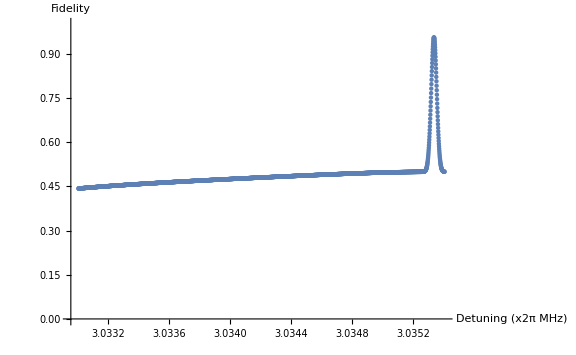
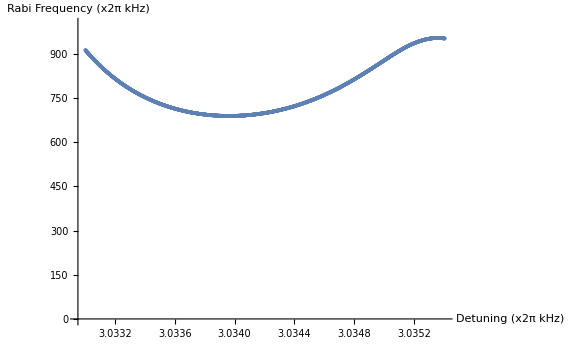

```mathematica
{Max[usweepres[[;;,1]]],#,Chop[(uArr[[#]](*-wmvals[[dirDJ,modeDJ]]*))/wmhz],Max[Abs[usweepres[[#,2]]]]/wkhz}&[First@Ordering[usweepres[[;;,1]],-1]]
usweepres[[%[[2]],2]]/wkhz
{Min[#],uArr[[Ordering[#,1]]]/wmhz}&[Max/@Abs[usweepres[[;;,2]]/wkhz]]
{ListPlot[usweepres[[;;,1]],DataRange->(uArr[[{1,-1}]](*-wmvals[[dirDJ,modeDJ]]*))/wmhz,PlotRange->{0,1},ImageSize->Large,AxesLabel->{"Detuning (x2π MHz)","Fidelity"}(*,PlotLabel->"Mode: "<>ToString[modeDJ]<>", Dir: "<>ToString[dirDJ]*)],ListPlot[Max/@Abs[usweepres[[;;,2]]/wkhz],DataRange->(uArr[[{1,-1}]](*-wmvals[[dirDJ,modeDJ]]*))/wmhz,PlotRange->{0,1000},ImageSize->Large,AxesLabel->{"Detuning (x2π kHz)","Rabi Frequency (x2π kHz)"}(*,PlotLabel->"Mode: "<>ToString[modeDJ]<>", Dir: "<>ToString[dirDJ]*)]}
```